```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/778nm.dat"]
```

{{1.45287,-0.0633765},{1.39708,-0.244942},{1.35876,-0.388859},{1.32403,-0.50218},{1.28662,-0.619191},{1.25869,-0.68393},{1.22636,-0.726311},{1.19613,-0.715577},{1.17366,-0.788535},{1.15413,-0.922711},{1.12528,-1.1405},{1.11495,-0.816581},{1.10625,-0.841949},{1.09912,-0.739568},{1.09306,-0.636786},{1.0888,-0.576752},{1.08648,-0.632673},{1.08572,-0.683078},{1.08632,-1.06959},{1.0888,-1.20207},{1.09505,-0.701421},{1.09559,-0.63828},{1.12528,-0.455659},{1.14263,-0.323779},{1.16354,-0.199317},{1.19414,-0.130975},{1.22405,-0.0878808},{1.25343,-0.0683752},{1.28081,-0.0555444},{1.31748,-0.045238},{1.36987,-0.0355754},{1.42194,-0.0281937},{1.47153,-0.0297481},{1.11308,-0.434853}}

-2.91006+1.98951 x

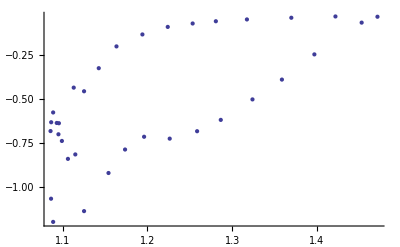

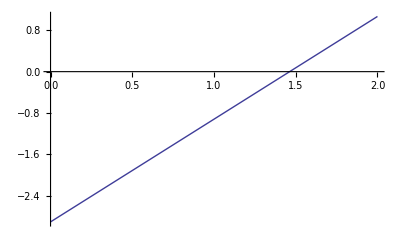

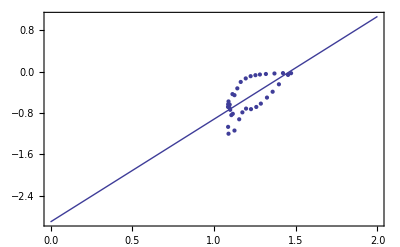

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```